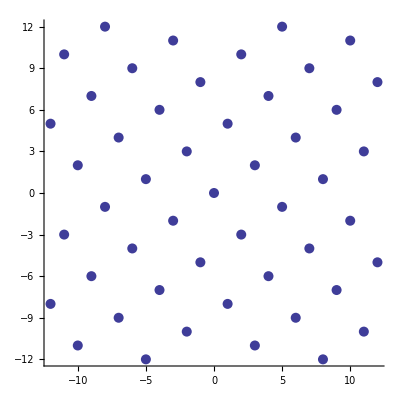

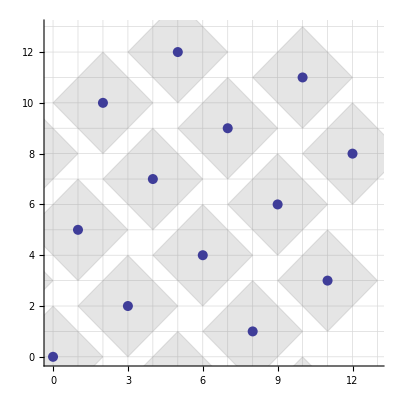

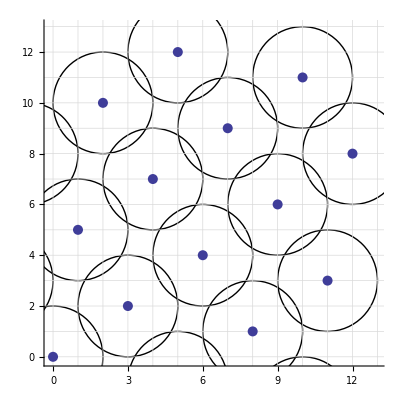

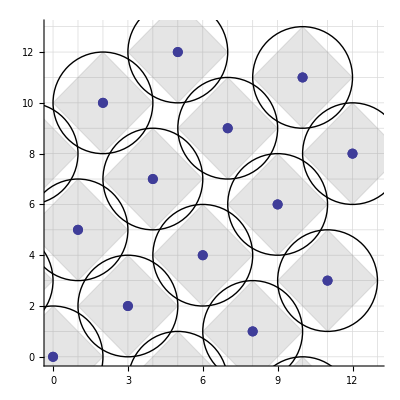

-Graphics-

-Graphics-

-Graphics-

```mathematica
v3={1, 5};
v4={0,13};
varMax=20;
Reticulado3=Select[Flatten[Table[i*v3+j*v4,{i,-varMax,varMax},{j,-varMax,varMax}],1],Max[Abs[#]]≤12&];
BolaLee[r_,c_]:=Graphics[{Thickness[0.005],Opacity[0.2],FaceForm[Gray ],EdgeForm[Directive[Gray]],Polygon[{c + {r,0},c+{0,r},c+{-r,0},c+{0,-r},c+{r,0}}]}];
Hexagonal1=ListPlot[Reticulado3,AspectRatio->1,Ticks->True,PlotStyle->PointSize[0.018]]
Bolas=Map[BolaLee[2,#]&,Reticulado3];

A=Show[Bolas,Hexagonal1,Axes->True,GridLines->{Range[0,14],Range[0,14]},PlotRange->{{-0.1,13},{-0.1,13}}]


BolaLee[c_,r_]:=Graphics[Circle[c,r]];
Bolas=Map[BolaLee[#,2]&,Reticulado3];

B=Show[Bolas,Hexagonal1,Axes->True,GridLines->{Range[0,14],Range[0,14]},PlotRange->{{-0.1,13},{-0.1,13}}]
Show[A,B]
```

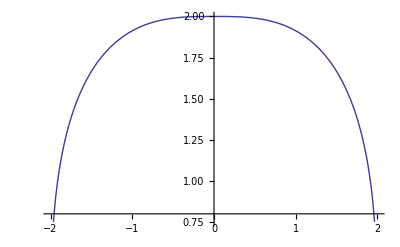

```mathematica
M1=Plot[(8-Abs[x]^3)^(1/3), {x,-8^(1/3), 8^(1/3)}]
```

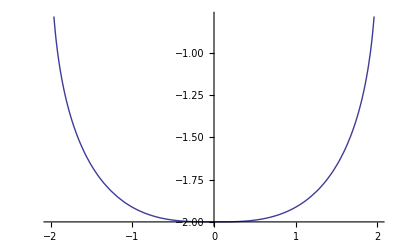

```mathematica
M2=Plot[-(8-Abs[x]^3)^(1/3), {x,-8^(1/3), 8^(1/3)}]
```

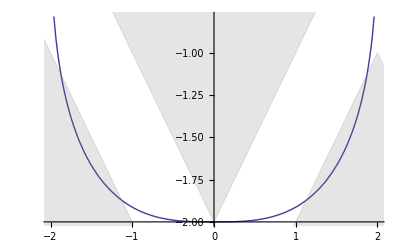

```mathematica
Show[M2,A,M1]
```

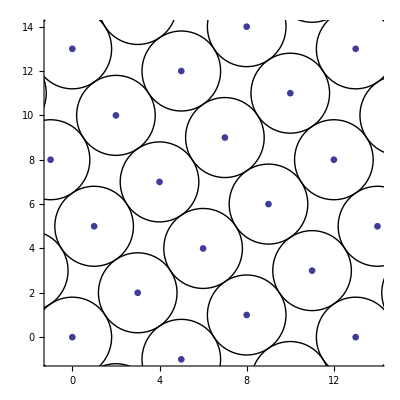

```mathematica
v3={1, 5};
v4={0,13};
varMax=20;
Reticulado4=Select[Flatten[Table[i*v3+j*v4,{i,-varMax,varMax},{j,-varMax,varMax}],1],Max[Abs[#]]≤20&];
BolaLee[c_,r_]:=Graphics[Circle[c,r]];
Hexagonal1=ListPlot[Reticulado4,AspectRatio->1,Ticks->True,PlotStyle->PointSize[0.012]];
Bolas=Map[BolaLee[#,1.8027756377319946]&,Reticulado3];

Show[Bolas,Hexagonal1,Axes->True,PlotRange->{{-1,14},{-1,14}}]
```

```mathematica
Sqrt[13]-1
```

```mathematica
(√13)/2
```

```mathematica
(√13)/2   //N
```

1.80278

```mathematica
1/2 (√13-1)//N
```

1.30278

```mathematica
√13-1/2//N
```

3.10555

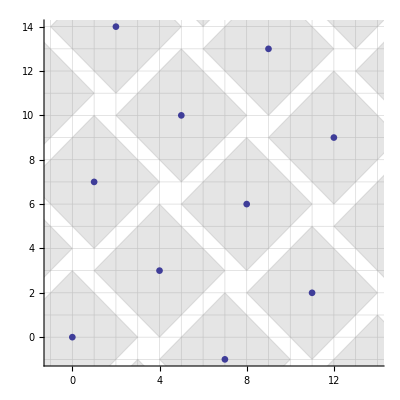

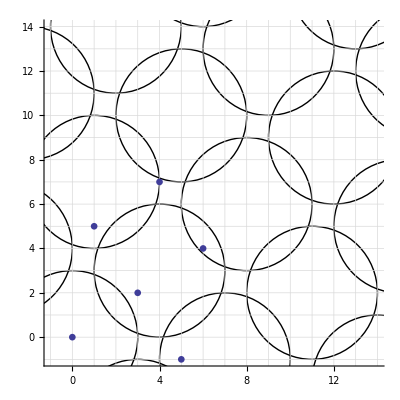

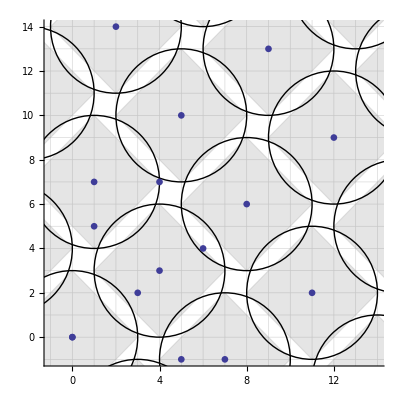

```mathematica
v3={1, 7};
v4={0,25};
varMax=20;
Reticulado3=Select[Flatten[Table[i*v3+j*v4,{i,-varMax,varMax},{j,-varMax,varMax}],1],Max[Abs[#]]≤20&];
BolaLee[r_,c_]:=Graphics[{Thickness[0.005],Opacity[0.2],FaceForm[Gray ],EdgeForm[Directive[Gray]],Polygon[{c + {r,0},c+{0,r},c+{-r,0},c+{0,-r},c+{r,0}}]}];
Hexagonal1=ListPlot[Reticulado3,AspectRatio->1,Ticks->True,PlotStyle->PointSize[0.012]];
Bolas=Map[BolaLee[3,#]&,Reticulado3];

A=Show[Bolas,Hexagonal1,Axes->True,GridLines->{Range[-1,14],Range[-1,14]},PlotRange->{{-1,14},{-1,14}}]

v3={1, 5};
v4={0,13};
varMax=20;
Reticulado4=Select[Flatten[Table[i*v3+j*v4,{i,-varMax,varMax},{j,-varMax,varMax}],1],Max[Abs[#]]≤7&];
BolaLee[c_,r_]:=Graphics[Circle[c,r]];
Hexagonal1=ListPlot[Reticulado4,AspectRatio->1,Ticks->True,PlotStyle->PointSize[0.012]];
Bolas=Map[BolaLee[#,3]&,Reticulado3];

B=Show[Bolas,Hexagonal1,Axes->True,GridLines->{Range[-1,14],Range[-1,14]},PlotRange->{{-1,14},{-1,14}}]
Show[A,B]
```

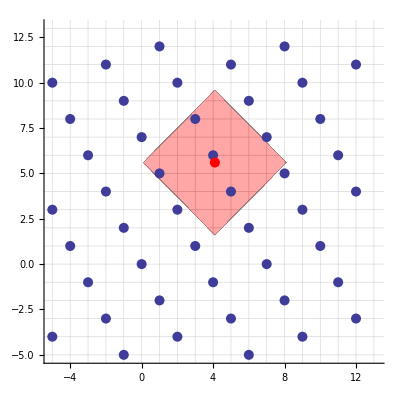

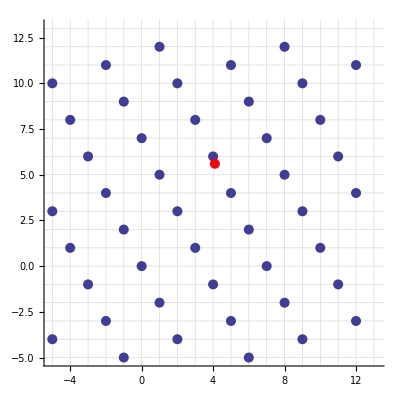

```mathematica
v3={1, 5};
v4={0,7};
varMax=20;
Reticulado3=Select[Flatten[Table[i*v3+j*v4,{i,-varMax,varMax},{j,-varMax,varMax}],1],Max[Abs[#]]≤12&];
BolaLee[r_,c_]:=Graphics[{Thickness[0.005],Opacity[0.004],FaceForm[Red ],EdgeForm[Directive[Gray]],Polygon[{c + {r,0},c+{0,r},c+{-r,0},c+{0,-r},c+{r,0}}]}];
Hexagonal1=ListPlot[Reticulado3,AspectRatio->1,Ticks->True,PlotStyle->PointSize[0.018]];
Bolas=Map[BolaLee[4,{4.1,5.6}]&,Reticulado3];
G={{4.1,5.6}};
G1=ListPlot[G,PlotStyle->Directive[ PointSize[0.018], Red]];
A=Show[Bolas,Hexagonal1,G1, Axes->True,GridLines->{Range[-5,14],Range[-5,14]},PlotRange->{{-5.1,13.2},{-5.1,13.1}}]
A=Show[Hexagonal1,G1, Axes->True,GridLines->{Range[-5,14],Range[-5,14]},PlotRange->{{-5.1,13.2},{-5.1,13.1}}]
```

```mathematica
v3={1, 0};
v4={1/2,Sqrt[3]/2};
varMax=20;
Reticulado1=Select[Flatten[Table[i*v3+j*v4,{i,-varMax,varMax},{j,-varMax,varMax}],1],Max[Abs[#]]≤12&];
Hexagonal1=ListPlot[Reticulado1,AspectRatio->1,Ticks->True,PlotStyle->Directive[Black,PointSize[0.018]]];

v5={1, 0};
v6={0,2*Sqrt[3]};
varMax=20;
Reticulado2=Select[Flatten[Table[i*v5+j*v6,{i,-varMax,varMax},{j,-varMax,varMax}],1],Max[Abs[#]]≤12&];
Hexagonal2=ListPlot[Reticulado2,AspectRatio->1,Ticks->True,PlotStyle->Directive[Gray,PointSize[0.018]]];

Show[Hexagonal1,Hexagonal2,PlotRange->{{-4.2,4.2},{-3.6,3.6}}]
```

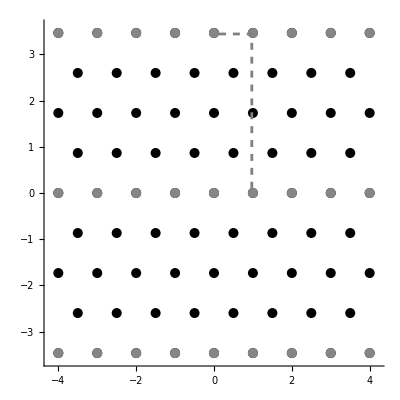

```mathematica
A={{0,0},{2,-2},{6,-2},{4,0},{2,2},{6,2},{8,0}}
B=ListPlot[A,AspectRatio->1,Axes->False,PlotStyle->Directive[Black,PointSize[0.018]]]
```

{{0,0},{2,-2},{6,-2},{4,0},{2,2},{6,2},{8,0}}

```mathematica
Exit[]
```

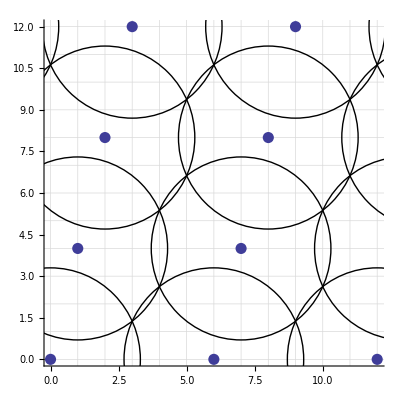

```mathematica
v3={1, 4};
v4={0,24};
varMax=30;
Reticulado4=Select[Flatten[Table[i*v3+j*v4,{i,-varMax,varMax},{j,-varMax,varMax}],1],Max[Abs[#]]≤30&];
BolaLee[c_,r_]:=Graphics[Circle[c,r]];
Hexagonal2=ListPlot[Reticulado4,AspectRatio->1,Ticks->True,PlotStyle->PointSize[0.02]];
Bolas=Map[BolaLee[#,3.3001]&,Reticulado4];

B=Show[Hexagonal2, Bolas,Axes->True,GridLines->{Range[-1,22],Range[-1,22]},PlotRange->{{0,12.01},{0,12}}]
```

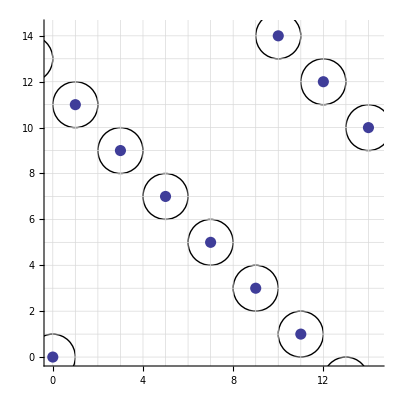

```mathematica
v3={1, 11};
v4={0,24};
varMax=20;
Reticulado3=Select[Flatten[Table[i*v3+j*v4,{i,-varMax,varMax},{j,-varMax,varMax}],1],Max[Abs[#]]≤20&];
BolaLee[c_,r_]:=Graphics[Circle[c,r]];
Hexagonal2=ListPlot[Reticulado3,AspectRatio->1,Ticks->True,PlotStyle->PointSize[0.02]];
Bolas=Map[BolaLee[#,1]&,Reticulado3];

B=Show[Bolas,Hexagonal2,Axes->True,GridLines->{Range[-1,14],Range[-1,14]},PlotRange->{{-0.1,14.4},{-0.1,14.4}}]
```

```mathematica
v3={1, 5};
v4={0,7};
varMax=20;
Reticulado3=Select[Flatten[Table[i*v3+j*v4,{i,-varMax,varMax},{j,-varMax,varMax}],1],Max[Abs[#]]≤12&];
BolaLee[r_,c_]:=Graphics[{Thickness[0.005],Opacity[0.004],FaceForm[Red ],EdgeForm[Directive[Red]],Polygon[{c + {r,0},c+{0,r},c+{-r,0},c+{0,-r},c+{r,0}}]}];
Hexagonal1=ListPlot[Reticulado3,AspectRatio->1,Ticks->True,PlotStyle->{Red,PointSize[0.018]}];
Bolas=Map[BolaLee[4,{4.1,5.6}]&,Reticulado3];
G={{4.1,5.6}};
G1=ListPlot[G,PlotStyle->Directive[ PointSize[0.018], Red]];
A=Show[Hexagonal1, Axes->True,GridLines->{Range[-11,14],Range[-12,13.1]},PlotRange->{{-10.8,10.8},{-11,11.1}}]
```

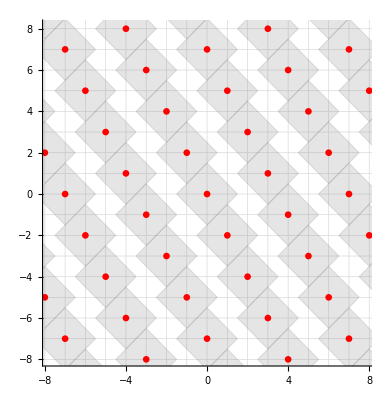

```mathematica
v3={1, 5};
v4={0,7};
varMax=20;
Reticulado3=Select[Flatten[Table[i*v3+j*v4,{i,-varMax,varMax},{j,-varMax,varMax}],1],Max[Abs[#]]≤20&];
BolaLee[r_,c_]:=Graphics[{Thickness[0.005],Opacity[0.2],FaceForm[Gray ],EdgeForm[Directive[Gray]],Polygon[{c + {r,0},c+{0,r},c+{-r,0},c+{0,-r},c+{r,0}}]}];
Hexagonal1=ListPlot[Reticulado3,AspectRatio->1,Ticks->True,PlotStyle->{Red,PointSize[0.012]}];
Bolas=Map[BolaLee[1.5,#]&,Reticulado3];

A=Show[Bolas,Hexagonal1,Axes->True,GridLines->{Range[-11,14],Range[-12,13.1]},PlotRange->{{-7.8,7.8},{-8,8.1}}]
```